```mathematica
f[x_,y_] := x^2+y^2+x y - 3
g[x_,y_]:=(x-1)^2+ (y-1)^2-x y^2-3
```

```mathematica
Subscript[f, x][x_,y_]:=D[f[x,y],x]
Subscript[f, y][x_,y_]:=D[f[x,y],y]
```

```mathematica
Subscript[g, x][x_,y_]:=D[g[x,y],x]
Subscript[g, y][x_,y_]:=D[g[x,y],y]
```

```mathematica
(*
	x:= x+(f[x,y] Subscript[g, y][x,y] - g[x,y]Subscript[f, y][x,y])/(Subscript[g, x][x,y]Subscript[f, y][x,y]-Subscript[f, x][x,y] Subscript[g, y][x,y])
y:= y+(g[x,y] Subscript[f, x][x,y] - f[x,y]Subscript[g, x][x,y])/(Subscript[g, x][x,y]Subscript[f, y][x,y]-Subscript[f, x][x,y] Subscript[g, y][x,y])
*)
```

```mathematica
u[x_,y_]:=(f[x,y] Subscript[g, y][x,y] - g[x,y]Subscript[f, y][x,y])/(Subscript[g, x][x,y]Subscript[f, y][x,y]-Subscript[f, x][x,y] Subscript[g, y][x,y])
v[x_,y_]:=(g[x,y] Subscript[f, x][x,y] - f[x,y]Subscript[g, x][x,y])/(Subscript[g, x][x,y]Subscript[f, y][x,y]-Subscript[f, x][x,y] Subscript[g, y][x,y])
```

```mathematica
Subscript[u, x][x_,y_]:=D[u[x,y],x]
Subscript[u, y][x_,y_]:=D[u[x,y],y]
```

```mathematica
Subscript[v, x][x_,y_]:=D[v[x,y],x]
Subscript[v, y][x_,y_]:=D[v[x,y],y]
```

```mathematica
Simplify[Solve[Nx==x+(u[x,y] Subscript[v, y][x,y] - v[x,y]Subscript[u, y][x,y])/(Subscript[v, x][x,y]Subscript[u, y][x,y]-Subscript[u, x][x,y] Subscript[v, y][x,y]) &&
Ny==y+ (v[x,y] Subscript[u, x][x,y] - u[x,y]Subscript[v, x][x,y])/(Subscript[v, x][x,y]Subscript[u, y][x,y]-Subscript[u, x][x,y] Subscript[v, y][x,y]),{Nx,Ny}]]
```

{{Nx→(x^6 (2+12 y+17 y^2+2 y^3)+2 x^5 (-24-49 y+33 y^2+61 y^3+3 y^4)-2 x^4 (-84-272 y-34 y^2+57 y^3-37 y^4+y^5)+x^2 (54+528 y+27 y^2-432 y^3-58 y^4+60 y^5-59 y^6)-4 x^3 (1+81 y-110 y^2-98 y^3+45 y^4+31 y^5+2 y^6)+4 y (-15-21 y-5 y^2+18 y^3+19 y^4+5 y^5-3 y^6+2 y^7)+2 x (30-21 y-135 y^2-93 y^3-119 y^4-55 y^5+39 y^6+17 y^7+y^8))/(2 x^6 (-3-4 y+6 y^2+4 y^3)+2 x^5 (10+28 y+y^4)-x^4 (8+36 y-122 y^2-60 y^3+47 y^4+28 y^5)-2 x^3 (-34-136 y+19 y^2+46 y^3-30 y^4+8 y^5+7 y^6)-2 y (84+159 y+106 y^2+109 y^3+80 y^4+23 y^5+14 y^6+y^7)+x^2 (-18-204 y+276 y^2+316 y^3-11 y^4+48 y^5+27 y^6+10 y^7)+x (96+480 y+222 y^2-88 y^3+60 y^4+40 y^5-6 y^6+8 y^7+4 y^8)),Ny→(-2 x^6 (2+12 y+17 y^2+2 y^3)+x^5 (12+58 y+48 y^2-73 y^3-3 y^4)+x^4 (-24-188 y-334 y^2-6 y^3-40 y^4+7 y^5)+2 x^3 (-44-78 y+70 y^2-125 y^3-48 y^4+19 y^5+2 y^6)+x^2 (12+192 y+54 y^2+708 y^3+572 y^4+33 y^5+28 y^6-3 y^7)-2 y (30+135 y+253 y^2+192 y^3+166 y^4+83 y^5+3 y^6+2 y^7)+x (60+186 y+636 y^2+375 y^3-25 y^4+124 y^5+42 y^6-5 y^7-y^8))/(2 x^6 (-3-4 y+6 y^2+4 y^3)+2 x^5 (10+28 y+y^4)-x^4 (8+36 y-122 y^2-60 y^3+47 y^4+28 y^5)-2 x^3 (-34-136 y+19 y^2+46 y^3-30 y^4+8 y^5+7 y^6)-2 y (84+159 y+106 y^2+109 y^3+80 y^4+23 y^5+14 y^6+y^7)+x^2 (-18-204 y+276 y^2+316 y^3-11 y^4+48 y^5+27 y^6+10 y^7)+x (96+480 y+222 y^2-88 y^3+60 y^4+40 y^5-6 y^6+8 y^7+4 y^8))}}

```mathematica
Bx[x_,y_]:= (x^6 (2+12 y+17 y^2+2 y^3)+2 x^5 (-24-49 y+33 y^2+61 y^3+3 y^4)-2 x^4 (-84-272 y-34 y^2+57 y^3-37 y^4+y^5)+x^2 (54+528 y+27 y^2-432 y^3-58 y^4+60 y^5-59 y^6)-4 x^3 (1+81 y-110 y^2-98 y^3+45 y^4+31 y^5+2 y^6)+4 y (-15-21 y-5 y^2+18 y^3+19 y^4+5 y^5-3 y^6+2 y^7)+2 x (30-21 y-135 y^2-93 y^3-119 y^4-55 y^5+39 y^6+17 y^7+y^8))/(2 x^6 (-3-4 y+6 y^2+4 y^3)+2 x^5 (10+28 y+y^4)-x^4 (8+36 y-122 y^2-60 y^3+47 y^4+28 y^5)-2 x^3 (-34-136 y+19 y^2+46 y^3-30 y^4+8 y^5+7 y^6)-2 y (84+159 y+106 y^2+109 y^3+80 y^4+23 y^5+14 y^6+y^7)+x^2 (-18-204 y+276 y^2+316 y^3-11 y^4+48 y^5+27 y^6+10 y^7)+x (96+480 y+222 y^2-88 y^3+60 y^4+40 y^5-6 y^6+8 y^7+4 y^8))
By[x_,y_]:= (-2 x^6 (2+12 y+17 y^2+2 y^3)+x^5 (12+58 y+48 y^2-73 y^3-3 y^4)+x^4 (-24-188 y-334 y^2-6 y^3-40 y^4+7 y^5)+2 x^3 (-44-78 y+70 y^2-125 y^3-48 y^4+19 y^5+2 y^6)+x^2 (12+192 y+54 y^2+708 y^3+572 y^4+33 y^5+28 y^6-3 y^7)-2 y (30+135 y+253 y^2+192 y^3+166 y^4+83 y^5+3 y^6+2 y^7)+x (60+186 y+636 y^2+375 y^3-25 y^4+124 y^5+42 y^6-5 y^7-y^8))/(2 x^6 (-3-4 y+6 y^2+4 y^3)+2 x^5 (10+28 y+y^4)-x^4 (8+36 y-122 y^2-60 y^3+47 y^4+28 y^5)-2 x^3 (-34-136 y+19 y^2+46 y^3-30 y^4+8 y^5+7 y^6)-2 y (84+159 y+106 y^2+109 y^3+80 y^4+23 y^5+14 y^6+y^7)+x^2 (-18-204 y+276 y^2+316 y^3-11 y^4+48 y^5+27 y^6+10 y^7)+x (96+480 y+222 y^2-88 y^3+60 y^4+40 y^5-6 y^6+8 y^7+4 y^8))
```

```mathematica
BpointList[x_,y_]:=N[NestWhileList[{Bx[#[[1]],#[[2]]],By[#[[1]],#[[2]]]}&,{x,y},Abs[#1[[1]]-#2[[1]]]>10^-5|| Abs[#1[[2]]-#2[[2]]]>10^-5&,2]]
BplotPoint[u_,v_]:=Show[ListPlot[BpointList[u,v],PlotStyle->Pink,PlotMarkers->{Automatic,Medium}],ContourPlot[{g[x,y] == 0, f[x,y] == 0}, {x,-4,4},{y,-4,4}, AxesLabel-> Automatic],PlotRange->{{u-1,u+1},{v-1,v+1}}]
```

{{0.,2.},{-0.251161,1.8168},{-0.232247,1.83612},{-0.232048,1.83638},{-0.232048,1.83638}}

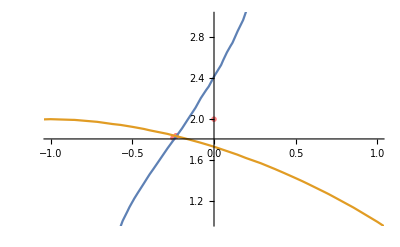

```mathematica
BpointList[0,2]
BplotPoint[0,2]
```

{{2.1,-1.1},{1.99874,-0.9947},{2.,-0.999995},{-4.,-4.},{4.06121,-3.74037},{1.17358,-1.22045},{2.23321,-0.554498},{1.98388,-1.16432},{1.99821,-1.00361},{1.99999,-1.00002},{2.16667,-0.916667},{2.3573,-0.837112},{1.65062,-1.05953},{1.98878,-0.994275},{1.99997,-0.999927},{1.99568,-0.999074},{2.,-1.00001},{0.,1.5},{-0.162788,1.77365},{-0.228646,1.83363},{-0.232041,1.83637},{-0.232048,1.83638}}

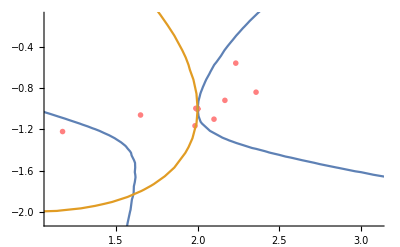

```mathematica
BpointList[2.1,-1.1]
BplotPoint[2.1,-1.1]
```

{{1.9,-0.9},{1.99817,-0.994339},{2.,-0.999993},{4.,-9.},{0.366886,-0.848102},{0.306479,-2.20844},{1.63109,-1.61363},{1.59728,-1.80887},{1.6038,-1.83644},{1.60433,-1.83638},{1.60433,-1.83638}}

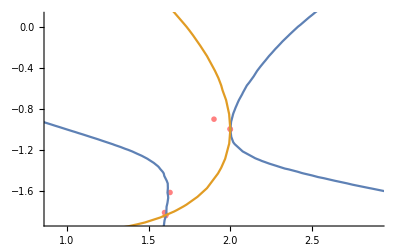

```mathematica
BpointList[1.9,-0.9]
BplotPoint[1.9,-0.9]
```

```mathematica
NSolve[{f[x,y]==0,g[x,y]==0},{x,y},Reals]
```

{{x→1.60433,y→-1.83638},{x→2.,y→-1.},{x→2.,y→-1.},{x→-0.232048,y→1.83638}}